## Part 1: Experimentation

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Graphics3D[Sphere[]]
```

-Graphics3D-

```mathematica
Table[x^2,{x,5,100, 5}]
```

{25,100,225,400,625,900,1225,1600,2025,2500,3025,3600,4225,4900,5625,6400,7225,8100,9025,10000}

```mathematica
f[x_,y_]:=x+y
f[4,a]
```

4+a

```mathematica
(#+1)&[50]
(#1+#2)&[20, 30]
```

51

50

```mathematica
Map[f,{a,b,c,d}]
f/@{a,b,c,d}
```

{f[a],f[b],f[c],f[d]}

{f[a],f[b],f[c],f[d]}

```mathematica
(#+1)&/@ {1,2,3}
```

{2,3,4}

```mathematica
(* Made-up problem: solve quadratic equation using quadratic formula *)
f[a_, b_, c_]:={(-b-Sqrt[b^2-4*a*c])/2, (-b+Sqrt[b^2-4*a*c])/2};
f[2,3,-1]
```

{1/2 (-3-√17),1/2 (-3+√17)}

## Part 2: Series Expansion

```mathematica
SerCos[x_,n_]:=Normal[Series[Cos[y],{y, 0, n}]]/.y->x
SerSin[x_,n_]:=Normal[Series[Sin[y],{y, 0, n}]]/.y->x
N[SerSin[x,10]-Sin[x]/.x->1]
N[SerSin[x,10]-Sin[x]/.x->2]
Plot[SerSin[x, 10]-Sin[x],{x,0,6Pi}]
```

2.48923×10^-8

0.0000500159

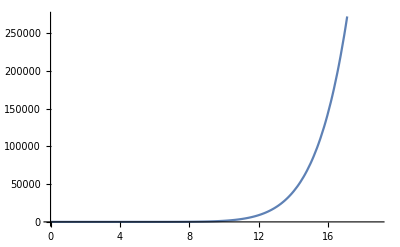

x^2-x^4/3

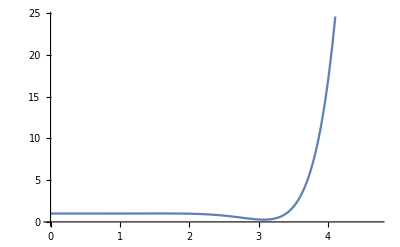

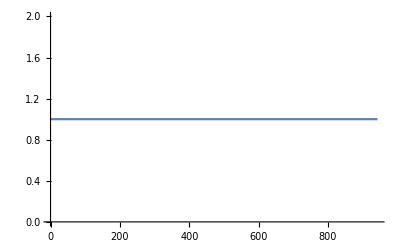

```mathematica
SerCosSq[x_, n_] := Normal[Series[Cos[y]^2,{y, 0, n}]]/.y->x
SerSinSq[x_, n_] := Normal[Series[Sin[y]^2,{y, 0, n}]]/.y->x
n=5;
SerSinSq[x,n]
Plot[SerCos[x, n]^2+SerSin[x, n]^2,{x,0,3Pi/2}]
Plot[SerCosSq[x, n]+SerSinSq[x, n],{x,0,300Pi}]
```

Doing (SerCos[x,n]^2 + SerSin[x,n]^2) diverges after a certain time (depending on n). Graphically/numerically, it stays around 1 before decreasing towards 0 and then diverging to positive infinity. Algebraically, we have the following (using n=5 as an example):

SerCos[x,5]^2 + SerSin[x,5]^2 =(1-1/2 x^2+1/24 x^4)^2+(x-1/6 x^3+1/120 x^5)^2=1+1/360 x^6-1/960 x^8+1/14400 x^10

As x increases, the tenth-degree polynomial diverges away from 1, since the x^10 term grows faster than the rest of the polynoimal. Thus, the sum goes to infinity as x goes to infinity.

In comparison, the sum (SerCosSq[x,n]^2 + SerSinSq[x,n]^2) stays at 1 forever. Expanding algebraically for n=5, we find the following:

SerCosSq[x,5] + SerSinSq[x,5] =(1-x^2+1/3 x^4)+ (x^2-1/3 x^4)=1

Thus, the trigonometric identity is true for SerCosSq + SerSinSq.

## Part 3: Euler Angles

```mathematica
(*1*)
Rx[theta_]:={{1,0,0},{0,Cos[theta],-Sin[theta]},{0,Sin[theta],Cos[theta]}}
Ry[zeta_]:={{Cos[zeta], 0, Sin[zeta]},{0, 1, 0}, {-Sin[zeta],0,Cos[zeta]}}
Rz[phi_]:={{Cos[phi],-Sin[phi],0},{Sin[phi],Cos[phi],0},{0,0,1}}
(*2*)
Rot3[psi_,theta_,phi_]=Simplify[Rz[psi].Rx[theta].Rz[phi]];
(*3*)
Rot3Inverse[psi_,theta_,phi_]=Simplify[Rz[-phi].Rx[-theta].Rz[-psi]];
Simplify[Rot3Inverse[psi, theta, phi].Rot3[psi, theta, phi]]
(*4*)
Simplify[Inverse[Rot3[psi, theta, phi]].Rot3[psi, theta, phi]]
Simplify[Inverse[Rot3[psi, theta, phi]] - Rot3Inverse[psi, theta, phi]]
```

{{1,0,0},{0,1,0},{0,0,1}}

{{1,0,0},{0,1,0},{0,0,1}}

{{0,0,0},{0,0,0},{0,0,0}}

From above, we can see that the inverse obtained by Mathematica’s built-in Inverse function and the inverse obtained by Rot3Inverse are equivalent, since their difference exactly corresponds to the zero matrix.